# Stereo All Tests

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
$Path=Append[$Path,FileNames["*",{Directory[]<>"\1DPackage"}]];
```

```mathematica
<<"pyramid1d`"
<<"lineTest`"
<<"pixelTest`"
```

## read

```mathematica
read[set_,num_,reduce_,corf_]:=Module[{ia,ib,id,rgb2d,reduire,clean,io,left,right,disp,occ, frame, base,fileleft,fileright},(

base="D:\MastersMathematica\Data\Sintel";

frame="frame_"<>num<>".png";
fileleft=corf<>"_left";
fileright=corf<>"_right";
left=FileNameJoin[{base,"training",fileleft,set,frame}];
right=FileNameJoin[{base,"training",fileright,set,frame}];
disp=FileNameJoin[{base,"training","disparities",set,frame}];
occ=FileNameJoin[{base,"training","occlusions",set,frame}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];
reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];
ia=reduire[ColorConvert[clean@Import[left],"GrayScale"],reduce];
ib=reduire[ColorConvert[clean@Import[right],"GrayScale"],reduce];
id=reduire[Image[
rgb2d[Flatten[N@ImageData[clean@Import[disp],"Byte"],{{3},{1},{2}}]]
],reduce]/reduce;
io=reduire[ColorConvert[clean@Import[occ],"GrayScale"],reduce];
read[{left,right,disp,occ},reduce]={ia,ib,id,io};

{ia,ib,id,io}
)];
```

## Data 1

```mathematica
d=1;

(* downscaling *)
r=2;

{ia,ib,id,io}=read["bamboo_1","0001",r,"clean"]
MinMax[id]

(* a reduction of 6 is {173,73} *)
(*{ia,ib,id,io}=ImageCrop[#,{173,73}]&/@{ia,ib,id,io}*)

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=150/r;
ny=301/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny},{nx,nx+102}]&/@{ia,ib,id,io}

move[im_,dx_]:=ImagePerspectiveTransformation[im,TranslationTransform[{dx,0}],DataRange->Full];
ic=move[ia,-10]

ImageDimensions[#]&/@{ia,ib,ic,id,io}
MinMax[id]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{0.136895,38.6009}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

{{103,1},{103,1},{103,1},{103,1},{103,1}}

{5.21531,7.57983}

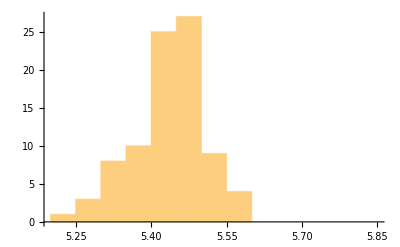

{5.21531,7.57983}

```mathematica
Histogram[Flatten[ImageData[id]]]
minmaxid=MinMax[Flatten[ImageData[id]]]
```

## Tests

```mathematica
pyr12=Flatten[{pyrFuncGen[ImageData[ia][[1]],5],pyrFuncGen[ImageData[ic][[1]],5]},{{2},{1},{3}}];
```

```mathematica
p=15;
lvlmin=1;
lvlmax=4;
```

```mathematica
error=0.01*2^(-lvlmax+1)
```

0.00125

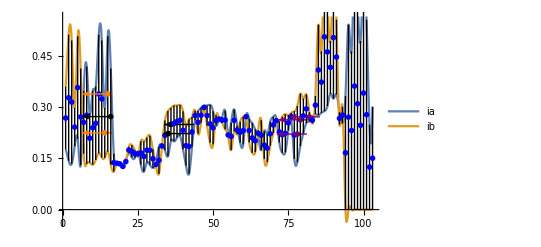
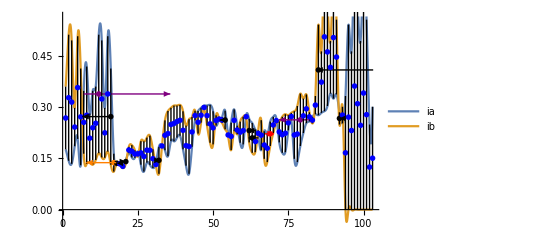

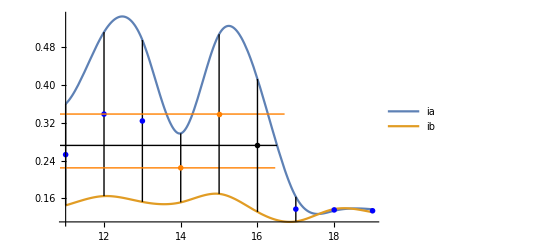

```mathematica
mode="Constrained";
Join[{lineTest[Range[1,Length[ImageData[ia][[1]]]],{lvlmin,lvlmax},pyr12,0.01,mode],lineTest[Range[1,Length[ImageData[ia][[1]]]],{lvlmin,lvlmin+1},pyr12,0.01,mode]}]
lineTest[Range[p-4,p+4],{lvlmin,lvlmax},pyr12,0.01,mode]
```

```mathematica
ListAnimate[pixelTest[p,20,lvlmax,pyr12[[lvlmin;; lvlmax]],0.006,mode]]
```